# Plotting Energy

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/smostaj1/ASU Dropbox/Setare MOSTAJABI SARHANGI/SummerSchool2024/Laboratories/Lab3/Analysis

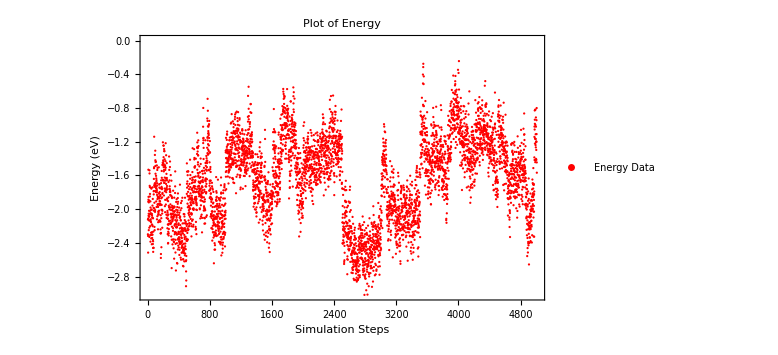

```mathematica
(*Import the data from the file*)
pE=Import["./ns/potentialE.dat"];

(*Determine the number of data points*)
npE=Length[pE];

(*Create a table of {x,y} pairs where x is the index and y is the value from pE*)
TpE=Table[{i,pE[[i,1]]},{i,npE}];

(*Plot the data with customized axes*)
pl1=ListPlot[TpE,PlotStyle->{Red,Thickness[0.01]},(*Set the color to red and line thickness*)
PlotRange->All,(*Include all data points in the plot range*)
Axes->True,(*Ensure axes are visible*)
FrameLabel->{"Simulation Steps","Energy (eV)"},
LabelStyle->Directive[FontSize->15],(*Set font size for labels*)
TicksStyle->Directive[FontSize->15],(*Set font size for ticks*)
PlotLabel->Style["Plot of Energy",FontSize->20,Bold],(*Set the title of the plot*)
PlotLegends->Placed[{"Energy Data"},{Right,Bottom}],(*Add and place the legend*)
Frame -> True,
ImageSize->Large (*Set the size of the plot*)];

(*Display the plot*)
pl1
```

v

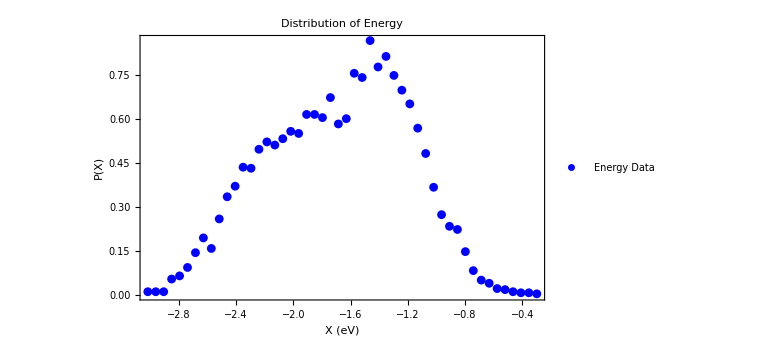

```mathematica
v(*Calculate the energy range and bin width*)
emin=Min[pE];
emax=Max[pE];
dE=(emax-emin)/50;
(*Bin the data and normalize*)
binCounts=BinCounts[pE,{emin,emax,dE}];
norm=Total[binCounts]*dE;
(*Prepare data for plotting*)
distData=Table[{emin+dE*(i-1),binCounts[[i]]/norm},{i,Length[binCounts]}];
(*Plot the distribution*)
distributionPlot=ListPlot[distData,PlotStyle->{Blue,Thickness[0.01]},
PlotRange->All,
Axes->True,
FrameLabel->{"X (eV)","P(X)"},
LabelStyle->Directive[FontSize->15],
TicksStyle->Directive[FontSize->15],
PlotLabel->Style["Distribution of Energy",FontSize->20,Bold],
PlotLegends->Placed[{"Energy Data"},{Right,Top}],
Frame->True,
ImageSize->Large]
(*Export the plot*)
Export["./Distribution-energy.png",distributionPlot,"PNG"];
Export["./Distribution-energy.pdf",distributionPlot,"PDF"];
```

```mathematica
binCounts
```

{3,3,3,15,18,26,40,54,44,72,93,103,121,120,138,145,142,148,155,153,171,171,168,187,162,167,210,206,241,216,226,208,194,181,158,134,102,76,65,62,41,23,14,11,6,5,3,2,2,1}

```mathematica
dE*2
```

0.11095

```mathematica
dE
```

0.0554748

```mathematica
dE+dE
```

0.11095

```mathematica
emin
 emin+dE
```

-3.01711

-2.96164

```mathematica
emin+dE
 emin+dE+dE
```

-2.96164

-2.90616